# DISCRETE FOURIER TRANSFORM

## ELE 489: DIGITAL SIGNAL PROCESSING LABORATORY

Due Date:

## Introduction

The DFT is without doubt the best known finite-length transform in use today. Its historical importance cannot be overstated. It is used to perform Fourier analysis of finite-duration sequences in many practical applications and the so-called Fast Fourier Transform (FFT) algorithm for computing the DFT is often cited as one of the most important computer algorithms of all time. In this short laboratory you will implement the DFT and IDFT transforms.

## Problem 1

The N-point discrete Fourier transform (DFT) of a finite-length real or complex sequence x[n] of length N is defined:

X[k] = ∑_(n=0)^(N-1) x[n] ⅇ^(- j (2π)/N k n),			k=0,1,...,N-1

The inverse discrete Fourier transform (IDFT) is given by

x[n] =1/N ∑_(k=0)^(N-1) X[k]  ⅇ^(j (2π)/N k n),		n=0,1,...,N-1

Write the code for the forward and inverse DFT transforms. Name the functions dft and idft, respectively. Each function should take one argument. For example, the input to the dft function should be list of samples of a sequence. The function should return a list of the same length containing the Fourier coefficients.

Write the code using Do or For loops.

## Problem 2

Obtain the DFTs of the following sequences:

(a). Random sequence, uniformly distributed:

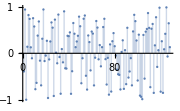

```mathematica
xa=RandomReal[{-1,1},128];
ListPlot[xa,Filling->0,PlotRange->All,ImageSize->Small]
```

What does the magnitude of the DFT of a random signal look like? Describe.

(b). Gaussian shaped sequence with noise:

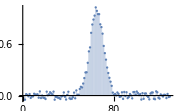

```mathematica
xb=GaussianMatrix[{{64},{6}}]/Max[GaussianMatrix[{{64},{6}}]]+RandomReal[{-0.05,0.05},129];
ListPlot[xb,Filling->0,PlotRange->All,ImageSize->Small]
```

What does the magnitude of the DFT of the Gaussian sequence look like? Describe.

(c) Multi-tone sinusoidal sequence:

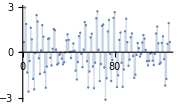

```mathematica
k=RandomInteger[{6,36},3];
xc=Table[Sin[(2.π)/135 k⟦1⟧ n]+3/2 Sin[(2.π)/150 k⟦2⟧ n]+2/3 Cos[(2.π)/155 k⟦3⟧ n],{n,0,127}];
ListPlot[xc,Filling->0,PlotRange->All,ImageSize->Small]
```

What does the magnitude of the DFT of the multi-tone sequence look like? Describe. How many DFT peaks do you see? How many should you see?

## Problem 3

Obtain the IDFTs of the following three complex sequences:

```mathematica
Xa=;
```

```mathematica
Xb=;
```

```mathematica
Xc=;
```

Compare the IDFTs with the sequence created below and comment on the results.

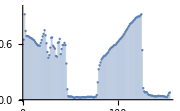

```mathematica
xd=PixelValue[-Graphics-,{80,All}];
ListPlot[xd,Filling->0,PlotRange->{0,1},ImageSize->Small]
```

## Problem 4

Measure and plot the execution time of your DFT code for N=2^n with n=4,5,...,12. How does the execution time change as the length of the signal is doubled?